```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/more_sectors

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

### Preliminaries famA

```mathematica
family = famA;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2,k3,k4},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
Union@Cases[intfam,_sp]
```

{}

```mathematica
intfam = {sp[k1,k1] + pp + 2 sp[k1,p]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2, sp[k2,k2]-m2, sp[k2,k2] + sp[k3,k3] + 2 sp[k2,k3]-m2, sp[k4,k4]-m2, sp[k3,k3] + sp[k4,k4]+2 sp[k3,k4] -m2,sp[k1,k2], sp[k1,k3], sp[k1,k4],sp[k3,k3] ,sp[k2,p], sp[k3,p],sp[k4,p],sp[k2,k4]};
Length[intfam]
```

14

```mathematica
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2,k3,k4},Directory->"famA"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];
UniqueSectors[family]
(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
(*SolvejSector/@UniqueSectors[family];

(*Save to disk*)
DiskSave[family];*)
```

famA is valid basis. The definitions of the basis will be saved in "famA" directory.
    Ds[famA] — denominators,
    SPs[famA] — scalar products involving loop momenta,
    LMs[famA] — loop momenta,
    EMs[famA] — external momenta,
    Parameters[famA] — parameters (invariants, masses, dimension),
    Toj[famA] — rules to transform scalar products to denominators,
    CutDs[famA] — flag vector of cut denominators.

famA

Identities are generated.
    IBP[famA] — integration-by-part identities,
    LI[famA] — Lorentz invariance identities.

$Aborted

FindSymmetries::noss: No sectors found. Forgot to analyze sectors with AnalyzeSectors[famA]?

UniqueSectors[famA]

```mathematica
tmp=UniqueSectors[famA];
tmp /. js[famA,a1_,a2_,a3_,a4_,a5_,a6_,bin__] /;Not[ FreeQ[{bin},1]] -> 0//Union
```

{0,js[famA,0,1,0,1,1,1,0,0,0,0,0,0,0,0],js[famA,0,1,1,1,1,1,0,0,0,0,0,0,0,0],js[famA,1,1,0,1,1,1,0,0,0,0,0,0,0,0],js[famA,1,1,1,0,1,1,0,0,0,0,0,0,0,0],js[famA,1,1,1,1,1,1,0,0,0,0,0,0,0,0]}

```mathematica
SolvejSector[{js[famA,0,1,0,1,1,1,0,0,0,0,0,0,0,0],js[famA,0,1,1,1,1,1,0,0,0,0,0,0,0,0],js[famA,1,1,0,1,1,1,0,0,0,0,0,0,0,0],js[famA,1,1,1,1,1,1,0,0,0,0,0,0,0,0]}]
DiskSave[family]
```

Sector js[famA,0,1,0,1,1,1,0,0,0,0,0,0,0,0]

Parameters {m2, pp, d} are assumed to be independent.

```mathematica
Get["./famA/famA"];
```

```mathematica
MIs[family]
```

{j[famA,0,1,0,1,1,1,0,0,0,0,0,0,0,0],j[famA,0,1,1,1,1,1,0,0,0,0,0,0,0,0],j[famA,1,1,0,1,1,1,0,0,0,0,0,0,0,0],j[famA,1,1,1,1,1,1,0,0,0,0,0,0,0,0]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family] 
sectors = %/.j[famA,a__] :> FromDigits[Reverse[{a}],2]
```

{j[famA,0,1,0,1,1,1,0,0,0,0,0,0,0,0],j[famA,0,1,1,1,1,1,0,0,0,0,0,0,0,0],j[famA,1,1,0,1,1,1,0,0,0,0,0,0,0,0],j[famA,1,1,1,1,1,1,0,0,0,0,0,0,0,0]}

{58,62,59,63}

```mathematica
(*4 tadpoles, 1 M*)
Import["./graphs/topoA/all/topoA_04_00027.dot"];
(*2 tadpoles * elliptic sunrise , 2 Masters *)
Import["./graphs/topoA/all/topoA_05_00031.dot"];
(* 4 masters, 4 loop banana *)
Import["./graphs/topoA/all/topoA_05_00059.dot"];
(*  tapole * 3 loop tadpole, 1 Masters  *)
Import["./graphs/topoA/all/topoA_05_00061.dot"];
(* top sector, 3 Masters  *)
Import["./graphs/topoA/all/topoA_06_00063.dot"];
```

```mathematica
(*topoA[1,1,0,1,1,0,0,0,0,0,0,0,0,0]
topoA[1,1,1,1,1,0,0,0,0,0,0,0,0,0]
D[topoA[1,1,1,1,1,0,0,0,0,0,0,0,0,0],pp]
topoA[1,1,0,1,1,1,0,0,0,0,0,0,0,0]
D[topoA[1,1,0,1,1,1,0,0,0,0,0,0,0,0],pp]
D[%,pp]
D[%,pp]
topoA[1,0,1,1,1,1,0,0,0,0,0,0,0,0]
topoA[1,1,1,1,1,1,0,0,0,0,0,0,0,0] + "2 more masters" *)
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
MppLiteRed/. m2 -> 1//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
(2-d)/((-4+pp) pp) | 0 | (4+(-4+d) pp)/(2 (-4+pp) pp) | 0
0 | (2-d)/((-4+pp) pp) | 0 | (4+(-4+d) pp)/(2 (-4+pp) pp))

```mathematica
(*MppLiteRed//MatrixPlot
Mm2LiteRed//MatrixPlot*)
```

```mathematica
listSectorA= Table[FromDigits[Reverse[(todiff[[i,2;;]]/. 2-> 1 /. j -> List) ],2], {i,1,Length[todiff]}]
```

{56,240,212,212,212,284,284,60,244,412,412,412,110,110,62,246,366,63,254,254}

```mathematica
Table[{todiff[[i]] /. 2-> 1,FromDigits[Reverse[(todiff[[i,2;;]]/. 2-> 1 /. j -> List) ],2], Total[todiff[[i,2;;]] /. 2-> 1/. j -> List]}, {i,1,Length[todiff]}]//TableForm
```

j[famA,0,0,0,1,1,1,0,0,0] | 56 | 3
j[famA,0,0,0,0,1,1,1,1,0] | 240 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,1,1,0,0,0,1] | 284 | 4
j[famA,0,0,1,1,1,0,0,0,1] | 284 | 4
j[famA,0,0,1,1,1,1,0,0,0] | 60 | 4
j[famA,0,0,1,0,1,1,1,1,0] | 244 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,1,1,1,0,1,1,0,0] | 110 | 5
j[famA,0,1,1,1,0,1,1,0,0] | 110 | 5
j[famA,0,1,1,1,1,1,0,0,0] | 62 | 5
j[famA,0,1,1,0,1,1,1,1,0] | 246 | 6
j[famA,0,1,1,1,0,1,1,0,1] | 366 | 6
j[famA,1,1,1,1,1,1,0,0,0] | 63 | 6
j[famA,0,1,1,1,1,1,1,1,0] | 254 | 7
j[famA,0,1,1,1,1,1,1,1,0] | 254 | 7

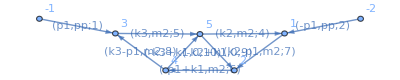

```mathematica
Import["./graphs/topoA/all/topoA_7_254.dot"]
```

### Start From d = 2

```mathematica
Dinv[j[famA,1,1,1,1,1,0,0,0,0,0,0,0,0,0],pp]
```

-j[famA,1,1,1,1,1,0,0,0,0,0,0,0,0,0]/(2 pp)+j[famA,2,0,1,1,1,0,0,0,0,0,0,0,0,0]/(2 pp)-j[famA,2,1,0,1,1,0,0,0,0,0,0,0,0,0]/(2 pp)-j[famA,2,1,1,1,1,0,-1,0,0,0,0,0,0,0]/pp-j[famA,2,1,1,1,1,0,0,0,0,0,0,0,0,0]+((-m2+pp) j[famA,2,1,1,1,1,0,0,0,0,0,0,0,0,0])/(2 pp)

```mathematica
mybasis = {(d-2)^4topoA[1,1,0,1,1,0,0,0,0,0,0,0,0,0], (* 4 tadpoles *)
(* sunrise *)
(d-2)^4 topoA[1,1,1,1,1,0,0,0,0,0,0,0,0,0],  (* elliptic sunrise * tadpole *)
(d-2)^4 Dinv[j[famA,1,1,1,1,1,0,0,0,0,0,0,0,0,0],pp] ,
(* banana 4 loops *)
topoA[1,1,0,1,1,1,0,0,0,0,0,0,0,0],
Dinv[j[famA,1,1,0,1,1,1,0,0,0,0,0,0,0,0],pp],
Dinv[Dinv[j[famA,1,1,0,1,1,1,0,0,0,0,0,0,0,0],pp],pp],
Dinv[Dinv[Dinv[j[famA,1,1,0,1,1,1,0,0,0,0,0,0,0,0],pp],pp],pp],
(* tadpole * three loop tadpole *)
topoA[1,0,1,1,1,1,0,0,0,0,0,0,0,0],
(* top sector *)
topoA[1,1,1,1,1,1,0,0,0,0,0,0,0,0] ,
topoA[1,1,1,1,1,1,-1,0,0,0,0,0,0,0],
topoA[1,1,1,1,1,1,-2,0,0,0,0,0,0,0]}/. j[famA,a__]-> INT[topoA,a] /. topoA[a__]-> INT[topoA,a];
mybasis=Collect[mybasis, {_INT}, Simplify];
```

```mathematica
todiff = Union@Cases[mybasis, _INT,∞] /. INT[topoA, a__] -> topoA[a];
todiff // Length
Export["./todiff.txt", todiff];
```

45

```mathematica
Derivate[elem_,s_]:=Module[{},Collect[Collect[Collect[elem, {_INT}, D[#,s]&] /.m2->1 , _INT, Factor]  +(( elem /. INT[a__] -> der[INT[a],s]) /. m2->1), _INT, Factor]]
```

```mathematica
derivative=Collect[Derivate[mybasis,pp], {_INT, _der}, Simplify];
```

### Build Basis start working in d = 2

```mathematica
remainingMastersInfo[[;;3,2]]
```

{topoB[-2,1,0,1,0,0,1,1,0],topoB[0,1,-2,1,0,0,1,1,0],topoB[0,1,0,1,0,0,1,1,0]}

```mathematica
Derivate[elem_,s_]:=Module[{},Collect[Collect[Collect[elem, {_INT}, D[#,s]&] /.m2->1 , _INT, Factor]  +(( elem /. INT[a__] -> der[INT[a],s])(* /. DEQ[s]*) /. m2->1), _INT, Factor]]
```

```mathematica
basisDone= {(d-2)j[famA,0,0,0,1,1,1,0,0,0], (* tadpole ^ 3    t = 3*)
 (-5+2 d)m2 j[famA,0,0,0,0,1,1,1,1,0], (* sunrise with two masses and no momentum  t = 4 *)
(* three MI sunrise*)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,0,1,0,1,1,0], (* banana with 2 equal masses  t = 3 *)
(d-2) j[famA,0,0,1,-1,1,0,1,1,0],
(d-2) j[famA,0,0,1,0,1,-1,1,1,0],
(* *)
(d-2)  j[famA,0,-1,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole     t = 4 *)
(d-2)Sqrt[pp] √(4 m2-pp) j[famA,0,0,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole   t = 4 *)
(* *)
(d-2)√pp √(4 m2-pp) j[famA,0,0,1,1,1,1,0,0,0], (* tadpole^2 * bubble   t = 4 *)
(* *)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,-1,1,1,1,1,0]} /. {j[famA,a__]:> INT[topoA, a],j[topoB,a__]:> INT[topoB, a]}
basisNew ={ m2 j[topoB,1,1,0,0,0,0,1,1,0] (* three loop tadpole *)
}
```

{(-2+d) INT[topoA,0,0,0,1,1,1,0,0,0],(-5+2 d) m2 INT[topoA,0,0,0,0,1,1,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,0,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,-1,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,0,1,-1,1,1,0],(-2+d) INT[topoA,0,-1,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,1,0,0,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,-1,1,1,1,1,0]}

{m2 j[topoB,1,1,0,0,0,0,1,1,0]}

```mathematica
nDone = Length[basisDone];
nNew = Length[basisNew];
basisToDiff= Join[basisDone, basisNew] /. {j[famA,a__]:> INT[topoA, a],j[topoB,a__]:> INT[topoB, a]};
```

```mathematica
basisDone[[;;5]] /. INT[topoA, a__]:> j[topoA,a]
```

{(-2+d) j[topoA,0,0,0,1,1,1,0,0,0],(-5+2 d) m2 j[topoA,0,0,0,0,1,1,1,1,0],(-2+d) √(4 m2-pp) √pp j[topoA,0,0,1,0,1,0,1,1,0],(-2+d) j[topoA,0,0,1,-1,1,0,1,1,0],(-2+d) j[topoA,0,0,1,0,1,-1,1,1,0]}

```mathematica
derUnred=(Derivate[basisToDiff,pp]//Simplify) /. √(-((-4+pp) pp))->Sqrt[(4 -pp)] Sqrt[pp] /. 1/ √(-((-4+pp) pp)) -> Sqrt[(4 -pp)] Sqrt[pp] /(4 -pp)/pp;
(* Collect integrals to diff *)
todiff=Join[Union@Cases[derUnred, _INT,∞],Union@Cases[basisToDiff, _INT,∞]];
Close["./todiff.inc"]
Do[WriteLine["todiff.inc",todiff[[i]]], {i,1,Length[todiff]}];
(* take derivative from reduze*)
deq=Import["./DEQ/deq.m"]/. {INT["topoA",a__,{bin__}]:> INT[topoA, bin],INT["topoB",a__,{bin__}]:> INT[topoB, bin]};
derUnred=Collect[derUnred /. deq, {_INT} ,Factor];
(* Collect integrals to reduze *)
toreduce=Join[Union@Cases[derUnred, _INT,∞],Union@Cases[basisToDiff, _INT,∞]];
Close["./to_reduce.inc"]
Do[WriteLine["to_reduce.inc",todiff[[i]]], {i,1,Length[todiff]}];
```

General::openx: ./todiff.inc is not open.

Close[./todiff.inc]

General::openx: ./to_reduce.inc is not open.

Close[./to_reduce.inc]

```mathematica
(* Import reduction from reduze*)
red=Import["./reductions/reduction.m"] /. {INT["topoA",a__,{bin__}]:> INT[topoA, bin],INT["topoB",a__,{bin__}]:> INT[topoB, bin]};
```

```mathematica
basisRed=Collect[basisToDiff /. red, {_INT}, Factor];
mis= Union@Cases[basisRed, _INT,∞]
Length[mis]
Length[basisRed]
(* basisRed = matBasis . mis *)
matBasis=CoefficientArrays[basisRed,mis][[2]]//Normal;
```

{INT[topoA,0,0,1,0,1,0,1,1,0],INT[topoA,0,0,1,0,1,0,2,1,0],INT[topoA,0,0,2,0,1,0,1,1,0],INT[topoA,0,1,1,0,0,0,1,1,0],INT[topoA,0,1,1,0,1,0,1,1,0],INT[topoA,0,1,1,1,0,0,1,0,0],INT[topoA,0,2,1,1,0,0,1,0,0],INT[topoA,1,1,1,0,0,0,0,0,0],INT[topoA,1,1,1,1,0,0,0,0,0],INT[topoB,1,1,0,0,0,0,1,1,0]}

10

10

```mathematica
(* reduze RHS*)
derRed=Collect[derUnred /.red, {_INT},Simplify] /. √(-((-4+pp) pp))->Sqrt[(4 -pp)] Sqrt[pp] /. 1/ √(-((-4+pp) pp)) -> Sqrt[(4 -pp)] Sqrt[pp] /(4 -pp)/pp;
test=Union@Cases[derRed[[;;]], _INT,∞];
Complement[test,mis]
```

{}

#### elliptic sector

```mathematica
SetDim[d];
Declare[
{p,k1,k2,k3},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
family2 = topoB;
intfam2  = {-m2+sp[k1,k1],-m2+sp[k2,k2],sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],sp[k3,k3]-2 sp[k3,p]+sp[p,p],sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3]-m2,sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3]-m2,pp+sp[k1,k1]+sp[k1,k2]-sp[k1,k3]-sp[k1,p]+sp[k2,k1]+sp[k2,k2]-sp[k2,k3]-sp[k2,p]-sp[k3,k1]-sp[k3,k2]+sp[k3,k3]+sp[k3,p]-sp[p,k1]-sp[p,k2]+sp[p,k3]}
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family2,intfam2,{k1,k2,k3},Directory->"topoB"]

GenerateIBP[family2];

AnalyzeSectors[family2];

FindSymmetries[family2];

(*(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector[js[topoB,0,1,0,1,0,0,1,1,0]];
(*Save to disk*)
DiskSave[family2];*)
```

{-m2+k1·k1,-m2+k2·k2,k3·k3,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2-2 k2·p,pp+k3·k3-2 k3·p,-m2+k1·k1-2 k1·k3+k3·k3,-m2+k2·k2-2 k2·k3+k3·k3,pp+k1·k1+2 k1·k2-2 k1·k3-2 k1·p+k2·k2-2 k2·k3-2 k2·p+k3·k3+2 k3·p}

topoB is valid basis. The definitions of the basis will be saved in "topoB" directory.
    Ds[topoB] — denominators,
    SPs[topoB] — scalar products involving loop momenta,
    LMs[topoB] — loop momenta,
    EMs[topoB] — external momenta,
    Parameters[topoB] — parameters (invariants, masses, dimension),
    Toj[topoB] — rules to transform scalar products to denominators,
    CutDs[topoB] — flag vector of cut denominators.

topoB

Identities are generated.
    IBP[topoB] — integration-by-part identities,
    LI[topoB] — Lorentz invariance identities.

Found 196(316) zero(nonzero) sectors out of 512.
    ZeroSectors[topoB] — zero sectors,
    NonZeroSectors[topoB] — nonzero sectors,
    SimpleSectors[topoB] — simple sectors (no nonzero subsectors),
    BasisSectors[topoB] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[topoB] — a rule to nullify all zero j[topoB…],
    CutDs[topoB] — a flag list of cut denominators (1=cut).

Found 236 mapped sectors and 80 unique sectors.
    UniqueSectors[topoB] — unique sectors.
    MappedSectors[topoB] — mapped sectors.
    SR[topoB][…] — symmetry relations for j[topoB,…] from UniqueSectors[topoB].
    jSymmetries[topoB,…] — symmetry rules for the sector js[topoB,…] in UniqueSectors[topoB].
    jRules[topoB,…] — reduction rules for j[topoB,…] from MappedSectors[topoB].
    SectorsMappings[topoB] gives the list of mappings of all sectors from MappedSectors[topoB] to UniqueSectors[topoB].

```mathematica
corner=j[topoB,0,1,0,1,0,0,1,1,0];
der1=Dinv[j[topoB,0,1,0,1,0,0,1,1,0],pp];
der2 = Dinv[der1,pp];
derder2 = Dinv[der2,pp];
```

```mathematica
Join[Cases[der1, _j,∞],Cases[der2, _j,∞],Cases[corner, _j,∞],Cases[derder2,_j,∞]]//Union
```

{j[topoB,-3,1,0,4,0,0,1,1,0],j[topoB,-2,1,0,3,0,0,1,1,0],j[topoB,-2,1,0,4,0,0,1,1,0],j[topoB,-1,1,0,2,0,0,1,1,0],j[topoB,-1,1,0,3,0,0,1,1,0],j[topoB,-1,1,0,4,0,0,1,1,0],j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,0,1,0,2,0,0,1,1,0],j[topoB,0,1,0,3,0,0,1,1,0],j[topoB,0,1,0,4,0,0,1,1,0]}

```mathematica
homogBasis = {corner, der1, der2};
```

```mathematica
RedPF=Import["./reductions/reduction_PF.m"] /. {INT["topoA",a__,{bin__}]:> INT[topoA, bin],INT["topoB",a__,{bin__}]:> INT[topoB, bin]}/. INT[fam_,a__]:> j[fam,a];
```

```mathematica
Union@Cases[RedPF[[;;,2]],_j,∞]
```

{j[topoA,1,1,1,0,0,0,0,0,0],j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,0,2,0,1,0,0,1,1,0],j[topoB,0,3,0,1,0,0,1,1,0]}

```mathematica
derder2RED=Collect[derder2 /. RedPF /. m2 -> 1, {_j},Factor];
```

```mathematica
inversion=Flatten[Solve[Thread[Equal[{mas1,mas2,mas3},Collect[homogBasis /. RedPF/.j[topoA,1,1,1,0,0,0,0,0,0]->0/.m2-> 1, {_j},Factor]]],{j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,0,2,0,1,0,0,1,1,0],j[topoB,0,3,0,1,0,0,1,1,0]}]];
```

```mathematica
Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}]
```

(mas1 (4-pp))/((-16+pp) (-4+pp) pp^2)+(mas2 (-64+68 pp-7 pp^2))/((-16+pp) (-4+pp) pp^2)-(6 mas3 (32-15 pp+pp^2))/((-16+pp) (-4+pp) pp)

```mathematica
HGM0
```

HGM0

```mathematica
HGM0 = {{0,1,0}, {0,0,1}, CoefficientArrays[Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}],{mas1,mas2,mas3}][[2]]//Normal};
```

```mathematica
dddPeriods = Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}] /. {mas1 -> period,mas2-> Dperiod,mas3 -> DDperiod}
```

(period (4-pp))/((-16+pp) (-4+pp) pp^2)+(Dperiod (-64+68 pp-7 pp^2))/((-16+pp) (-4+pp) pp^2)-(6 DDperiod (32-15 pp+pp^2))/((-16+pp) (-4+pp) pp)

```mathematica
(* third derivative MI = ..*)
PF=Collect[1/pp^3 (θ^3 -3 θ^2 +2   θ)-Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}] /. {  mas2 -> 1/pp θ, mas3 -> 1/pp^2(θ^2-θ) , d3MI -> 1/pp^3 (θ^3 -3 θ^2 +2   θ)}/.mas1-> 1/. pp -> λ//Simplify, {θ}, Simplify]
```

θ^3/λ^3+1/((-16+λ) λ^2)+(3 θ^2 (-10+λ))/((-16+λ) (-4+λ) λ^2)+(3 θ (-6+λ))/((-16+λ) (-4+λ) λ^2)

```mathematica
(* θ^3/λ^3+1/((-16+λ) λ^2)+(3 θ^2 (-10+λ))/((-16+λ) (-4+λ) λ^2)+(3 θ (-6+λ))/((-16+λ) (-4+λ) λ^2) correct, checked with Felix and Christoph *)
```

```mathematica
(* this is the derivative operator in lambada = m2 *)
OP =Collect[(-  Collect[λ^3(-16+λ) (-4+λ)  PF , {θ},Together] /.{θ^3-> F[θ,θ,θ], θ θ-> F[θ,θ] ,  θ-> F[θ]}  //Expand) , _F, Factor]
(* generically, if we want to shift λ = λ0 + ρ and expand around ρ ~ 0 (λ ~ λ0), the transformation is the following *)
OPlambda0 =Collect[ Collect[OP   /. {F[θ] -> F[θ] (1 + λ0/ρ) ,F[θ,θ] ->((λ0+ρ) (-λ0 F[θ]+(λ0+ρ) F[θ,θ]))/ρ^2, λ  -> λ0 +ρ }, {_F}, Simplify], {_F} ,Simplify];
(* choose here a point *)
toapply=(OPlambda0/. λ0 ->0/. F -> F1)//Simplify//Expand
(* indicial equation*)
Print["indicial equation:  ",( toapply /. ρ ->  0) == 0 ]
(* indices 0 *)
```

-((-4+λ) λ)-3 (-6+λ) λ F[θ]-3 (-10+λ) λ F[θ,θ]-(-16+λ) (-4+λ) F[θ,θ,θ]

4 ρ-ρ^2+18 ρ F1[θ]-3 ρ^2 F1[θ]+30 ρ F1[θ,θ]-3 ρ^2 F1[θ,θ]-64 F1[θ,θ,θ]+20 ρ F1[θ,θ,θ]-ρ^2 F1[θ,θ,θ]

indicial equation:  -64 F1[θ,θ,θ]==0

```mathematica
(* combine string of operators. F1 will be in the operator, F2 in the ansatz *)
combineOperator = { F1[a__]F2[b__] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
SolveForAnsatzMUM[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,coeffSol,der,derpoly,derpolyLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
Return[{sol0,sol1, coeffSol}];
]
```

```mathematica
SolveForAnsatzMUM3[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,sol2,coeffSol,der,derpoly,derpolyLog,derpolyLogLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+
 Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
(*third solution*)
ansatz =Sum[a[n] F2[g[log,2], g[ρ,n+indicial]]/2, {n,0,maxorder}]+ 
Sum[b[n]F2[g[log,1],g[ρ,n+indicial]], {n,1,maxorder}]+
Sum[c[n]F2[g[ρ,n+indicial]], {n,2,maxorder}] ; 
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
derpolyLogLog=Coefficient[der,log,2];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
(*Print[{Coefficient[derpoly,ρ,i+indicial],Coefficient[derpoly,ρ,i+indicial]/.coeffSol}];*)
coeffSol = Join[coeffSol,tmp], {i,2,maxorder}];
sol2 =Sum[a[n] F2[g[log,2], g[ρ,n+indicial]]/2, {n,0,maxorder}]+
 Sum[b[n]F2[g[log,1],g[ρ,n+indicial]], {n,1,maxorder}]+
Sum[c[n]F2[g[ρ,n+indicial]], {n,2,maxorder}] /. coeffSol;
Return[{sol0,sol1,sol2, coeffSol}];
]
```

```mathematica
point = 0;
maxorder=40
{sol[point][0],sol[point][1],sol[point][2], coeffSol[point]}=SolveForAnsatzMUM3[0,maxorder,0,toapply];
```

40

```mathematica
(* checked with Forner - Nega *)
s1 /. extractPolySol /. ρ^b_ /; b > 4 ->0
s2 /. extractPolySol /. ρ^b_ /; b > 4 ->0 /. L -> 0
s3 /. extractPolySol /. ρ^b_ /; b > 4 ->0 /.L-> 0
```

s1

s2

s3

```mathematica
(*Export["./PERIODS/omega012.m",{ω0[ρ]->sol[point][0]/.extractPolySol,ω1[ρ]->sol[point][1]/.extractPolySol,ω2[ρ]->sol[point][2]/.extractPolySol, coeffSol[point]}]
Export["./PERIODS/Domega0.m",{D[ω0[ρ],ρ]-> D[sol[point][0]/.extractPolySol,ρ]}]
Export["./PERIODS/DDomega0.m",{D[D[ω0[ρ],ρ],ρ]-> D[D[sol[point][0]/.extractPolySol,ρ],ρ]}]*)
```

```mathematica
(* check the solution up to the requested order *)
(Series[Expand[toapply sol[point][0]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP, {ρ,0,maxorder-1}]//Normal) /. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][1]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, 
{ρ,0,maxorder-1}]//Normal)/. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][2]]  //. combineOperator //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, {ρ,0,maxorder-1}]//Normal)/. ρ^(a_)/; a> 99 :> 0
```

0

0

0

```mathematica
(* Griffiths transversality condition (don't remember where they come from) *)
Σ = {{0,0,1},{0,-1,0}, {1,0,0}}
Print[{ω0,ω1,ω2}.Σ.{ω0,ω1,ω2}]
```

{{0,0,1},{0,-1,0},{1,0,0}}

-ω1^2+2 ω0 ω2

```mathematica
(*(* entry (1,1) *)
Collect[{ω0,ω1,ω2}.Σ.{ω0,ω1,ω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} , {L,ρ}]  /. ρ^n_/; n> 40 -> 0
(* entry (1,2) *)
Collect[{ω0,ω1,ω2}.Σ.{dω0,dω1,dω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> maxorder-1 -> 0
(* entry (1,3) = (3,1) *)
Collect[{ω0,ω1,ω2}.Σ.{ddω0,ddω1,ddω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 5-1 -> 0;
Series[(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-16+ ρ)(-4+ρ)ρ^2)/.{n[0]->64, n[1]-> 0,n[2]->0,n[3]-> 0}, {ρ,0,3}];
(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-16+ ρ)(-4+ρ)ρ^2)/.{n[0]->64, n[1]-> 0,n[2]->0,n[3]-> 0}
(* entry (2,3) = (3,2) *)
Collect[{dω0,dω1,dω2}.Σ.{ddω0,ddω1,ddω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 12-1 -> 0;
Series[% ((ρ^3)(ρ-4)^2(ρ-16)^2 ), {ρ,0,10} ];
Collect[Series[(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)^2(ρ-16)^2 )/.{n[0]->4096,n[1]->-1920,n[2] ->128}, {ρ,0,4}],ρ];
(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)^2(ρ-16)^2 )/.{n[0]->4096,n[1]->-1920,n[2] ->128}//FullSimplify;
(* entry (2,2) = (2,2) *)
Collect[{dω0,dω1,dω2}.Σ.{dω0,dω1,dω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 12-1 -> 0;
Series[% ((ρ^3)(ρ-4)(ρ-16) ), {ρ,0,10} ];
Collect[Series[(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)(ρ-16) )/.{n[0]->0,n[1]->-64,n[2]-> 0}, {ρ,0,4}],ρ];
(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)(ρ-16) )/.{n[0]->0,n[1]->-64,n[2]-> 0}//FullSimplify;
(* entry (3,3) = (3,3) *)
Collect[{ddω0,ddω1,ddω2}.Σ.{ddω0,ddω1,ddω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 12-1 -> 0;
Series[% ((ρ^4)(ρ-4)^3(ρ-16)^3 ), {ρ,0,10} ]
Collect[Series[(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)(ρ-16) )/.{n[0]->0,n[1]->-64,n[2]-> 0}, {ρ,0,4}],ρ];
-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4);*)
```

```mathematica
Z= {{0,0,64/((-16+ρ) (-4+ρ) ρ^2)},{0,-64/(ρ^2 (64-20 ρ+ρ^2)),(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3)},{64/((-16+ρ) (-4+ρ) ρ^2),(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3),-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4)}};
(* Agrees with Nega - Forner *)
(*Inverse[Z]64//Simplify//MatrixForm*)
```

```mathematica
W= {{ω0,ω1,ω2},{dω0,dω1,dω2},{ddω0,ddω1,ddω2}}
```

{{ω0,ω1,ω2},{dω0,dω1,dω2},{ddω0,ddω1,ddω2}}

```mathematica
putArgument = {ω1 ->ω1[ρ],dω1 ->D[ω1[ρ],ρ],ddω1 ->D[D[ω1[ρ],ρ],ρ],ω2 ->ω2[ρ],dω2 ->D[ω2[ρ],ρ],ddω2->D[D[ω2[ρ],ρ],ρ],ω0 ->ω0[ρ],dω0 ->D[ω0[ρ],ρ],ddω0 ->D[D[ω0[ρ],ρ],ρ]};
removeArgument=putArgument /. Rule[a_,b_]:> Rule[b,a];
```

```mathematica
eqs=Thread[Equal[(Flatten[W.Σ.Transpose[W]]// Simplify),Flatten[Z]]]//Union;
eqs=eqs /. {ω1 ->ω1[ρ],dω1 ->D[ω1[ρ],ρ],ddω1 ->D[D[ω1[ρ],ρ],ρ],ω2 ->ω2[ρ],dω2 ->D[ω2[ρ],ρ],ddω2->D[D[ω2[ρ],ρ],ρ],ω0 ->ω0[ρ],dω0 ->D[ω0[ρ],ρ],ddω0 ->D[D[ω0[ρ],ρ],ρ] };
eqs //TableForm
(* the second is the derivative of the third, the fifth is the derivative of the sixth, 
the fourth and the third combine into the derivative of the fifth.  *)
```

-ω1''[ρ]^2+2 ω0''[ρ] ω2''[ρ]==-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4)
ω2'[ρ] ω0''[ρ]-ω1'[ρ] ω1''[ρ]+ω0'[ρ] ω2''[ρ]==(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3)
-ω1'[ρ]^2+2 ω0'[ρ] ω2'[ρ]==-64/(ρ^2 (64-20 ρ+ρ^2))
ω2[ρ] ω0''[ρ]-ω1[ρ] ω1''[ρ]+ω0[ρ] ω2''[ρ]==64/((-16+ρ) (-4+ρ) ρ^2)
ω2[ρ] ω0'[ρ]-ω1[ρ] ω1'[ρ]+ω0[ρ] ω2'[ρ]==0
-ω1[ρ]^2+2 ω0[ρ] ω2[ρ]==0

```mathematica
eqstmp=eqs /. {ω0'[ρ] -> dω0,ω1'[ρ] -> dω1,ω2'[ρ] -> dω2,ω0[ρ] -> ω0,ω1[ρ] -> ω1,ω2[ρ] -> ω2,ω1''[ρ]-> ddω1,ω2''[ρ]-> ddω2,ω0''[ρ]-> ddω0}
```

{-ddω1^2+2 ddω0 ddω2==-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4),ddω2 dω0-ddω1 dω1+ddω0 dω2==(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3),-dω1^2+2 dω0 dω2==-64/(ρ^2 (64-20 ρ+ρ^2)),ddω2 ω0-ddω1 ω1+ddω0 ω2==64/((-16+ρ) (-4+ρ) ρ^2),dω2 ω0-dω1 ω1+dω0 ω2==0,-ω1^2+2 ω0 ω2==0}

```mathematica
sols=Flatten[Solve[eqstmp, {ddω0, ddω1,ddω2, dω1, dω2, ω2}]//Simplify]//PowerExpand//Simplify;
Collect[sols[[1]]/. Rule[a_,b_]:> a-b, {ddω0, ω0,dω0 }];
(* Relations for second derivative of omega0 *)
(*der2Omega0= ddω0->-(2 dω0 (32-15 ρ+ρ^2))/(ρ (64-20 ρ+ρ^2))+dω0^2/(2 ω0)-((-8+ρ) ω0)/(2 ρ (64-20 ρ+ρ^2))/.putArgument
Export["./PERIODS/der2Omega0.m", der2Omega0];*)
der2Omega0 = Import["./PERIODS/der2Omega0.m"];
```

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1, ω1/ω0,  1/2( ω1/ω0)^2},{0,1,  ω1/ω0}, {0,0,1}}
Wss = {{ω0,0,0},{dω0,-8/(ρ √(64-20 ρ+ρ^2)),0}, {ddω0,(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0),+64/(ρ^2 (64-20 ρ+ρ^2) ω0)}} 
replacements = {ω1^2/(2 ω0) -> ω2,(dω0 ω1)/ω0->dω1+8/(ρ √(64-20 ρ+ρ^2)) ,(dω0 ω1^2)/(2 ω0^2)->dω2+(8 ω1)/(ρ √(64-20 ρ+ρ^2) ω0)}
(*(Wss.Wu//.replacements//Simplify)/.replacements//MatrixForm*)
```

{{1,ω1/ω0,ω1^2/(2 ω0^2)},{0,1,ω1/ω0},{0,0,1}}

{{ω0,0,0},{dω0,-8/(ρ √(64-20 ρ+ρ^2)),0},{ddω0,(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0),64/(ρ^2 (64-20 ρ+ρ^2) ω0)}}

{ω1^2/(2 ω0)→ω2,(dω0 ω1)/ω0→dω1+8/(ρ √(64-20 ρ+ρ^2)),(dω0 ω1^2)/(2 ω0^2)→dω2+(8 ω1)/(ρ √(64-20 ρ+ρ^2) ω0)}

```mathematica
(*Last two entries needs some manipulations to verify *)
```

```mathematica
(*(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0)+(ddω0 ω1)/ω0//.ddω0->(dω0^2 ρ (64-20 ρ+ρ^2)-4 dω0 (32-15 ρ+ρ^2) ω0-(-8+ρ) ω0^2)/(2 ρ (64-20 ρ+ρ^2) ω0)//Simplify;
Collect[Collect[%, {ω0,dω0}]/.{(dω0^2 ω1)/(2 ω0^2)-> ddω1+1/2 (+(4 dω0 (4 √(64-20 ρ+ρ^2)+(32-15 ρ+ρ^2) ω1))/(ρ (64-20 ρ+ρ^2) ω0)-(1024 √(64-20 ρ+ρ^2)+32 ρ^2 (√(64-20 ρ+ρ^2)-7 ω1)+28 ρ^3 ω1-ρ^4 ω1+ρ (-480 √(64-20 ρ+ρ^2)+512 ω1))/(ρ^2 (64-20 ρ+ρ^2)^2))},{ω0,dω0},Simplify]*)
```

```mathematica
(*+64/(ρ^2 (64-20 ρ+ρ^2) ω0)-(8 dω0 ω1)/(√((-16+ρ) (-4+ρ)) ρ ω0^2)+(16 (32+(-15+ρ) ρ) ω1)/(((-16+ρ) (-4+ρ))^(3/2) ρ^2 ω0)+(ddω0 ω1^2)/(2 ω0^2)//.ddω0->(dω0^2 ρ (64-20 ρ+ρ^2)-4 dω0 (32-15 ρ+ρ^2) ω0-(-8+ρ) ω0^2)/(2 ρ (64-20 ρ+ρ^2) ω0)//Simplify;
Collect[%, {ω0,dω0}]
Collect[Collect[% ,{ω0,dω0}]/.(dω0^2 ω1^2)/(4 ω0^3)->ddω2-(256 √(64-20 ρ+ρ^2)+64 (32-15 ρ+ρ^2) ω1-(-8+ρ) ρ √(64-20 ρ+ρ^2) ω1^2)/(4 ρ^2 (64-20 ρ+ρ^2)^(3/2) ω0)+(dω0 ω1 (ρ^2 (8+√(64-20 ρ+ρ^2) ω1)+32 (16+√(64-20 ρ+ρ^2) ω1)-5 ρ (32+3 √(64-20 ρ+ρ^2) ω1)))/(ρ (64-20 ρ+ρ^2)^(3/2) ω0^2),{ω0,dω0},Simplify]*)
```

```mathematica
Wss//MatrixForm
```

(ω0 | 0 | 0
dω0 | -8/(ρ √(64-20 ρ+ρ^2)) | 0
ddω0 | (16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0) | 64/(ρ^2 (64-20 ρ+ρ^2) ω0))

```mathematica
(*
Inverse
*)
InvWss=Collect[Inverse[Wss]/.putArgument /. der2Omega0 /. removeArgument, {ω0, dω0, ddω0},FullSimplify](*//MatrixForm*)
```

{{1/ω0,0,0},{(dω0 √((-16+ρ) (-4+ρ)) ρ)/(8 ω0),-1/8 √((-16+ρ) (-4+ρ)) ρ,0},{(dω0^2 (-16+ρ) (-4+ρ) ρ^2)/(128 ω0)+1/128 (-8+ρ) ρ ω0,-1/64 dω0 (-16+ρ) (-4+ρ) ρ^2+(ρ+1/32 (-15+ρ) ρ^2) ω0,1/64 (-16+ρ) (-4+ρ) ρ^2 ω0}}

```mathematica
(*der3Omega0=D[D[D[ω0[ρ],ρ],ρ],ρ]->dddPeriods/.pp -> ρ /. {period  -> ω0[ρ],Dperiod-> D[ω0[ρ],ρ],DDperiod-> D[D[ω0[ρ],ρ],ρ] }
Export["./PERIODS/der3Omega0.m", der3Omega0]*)
der3Omega0=Import["./PERIODS/der3Omega0.m"];
```

```mathematica
InvWss
```

{{1/ω0,0,0},{(dω0 √((-16+ρ) (-4+ρ)) ρ)/(8 ω0),-1/8 √((-16+ρ) (-4+ρ)) ρ,0},{(dω0^2 (-16+ρ) (-4+ρ) ρ^2)/(128 ω0)+1/128 (-8+ρ) ρ ω0,-1/64 dω0 (-16+ρ) (-4+ρ) ρ^2+(ρ+1/32 (-15+ρ) ρ^2) ω0,1/64 (-16+ρ) (-4+ρ) ρ^2 ω0}}

```mathematica
derinvWss=Collect[D[InvWss /. putArgument,ρ] /. der3Omega0/.der2Omega0, {_ω0},Simplify] ;
```

```mathematica
(*test= derinvWss*)
```

```mathematica
Series[der2Omega0 /. Rule[a_,b_]-> a-b /. removeArgument /. ω0 -> sol[0][0] /.extractPolySol /. dω0  ->(  D[sol[0][0] /.extractPolySol,ρ])/.ddω0  ->(  D[D[sol[0][0] /.extractPolySol,ρ],ρ]), {ρ,0,2}]
Series[der3Omega0 /. Rule[a_,b_]-> a-b /. removeArgument  /.Derivative[3][ω0][ρ] ->( D[ D[D[sol[0][0] /.extractPolySol,ρ],ρ],ρ])/. ω0 -> sol[0][0] /.extractPolySol /. dω0  ->(  D[sol[0][0] /.extractPolySol,ρ])/.ddω0  ->(  D[D[sol[0][0] /.extractPolySol,ρ],ρ]) , {ρ,0,4}]
```

O[ρ]^3

O[ρ]^5

```mathematica
Print["new basis is J,  I = Wss J"]
```

new basis is J,  I = Wss J

```mathematica
(*(Solve[(pf /. m2 -> λ /. λ ->  ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten)*)
```

```mathematica
tmp1=(derinvWss.Wss /.putArgument /.der2Omega0/. removeArgument// Simplify )/.removeArgument;
tmp2=(InvWss.HGM0.Wss /.putArgument /.der2Omega0/. removeArgument// Simplify )/. pp -> ρ//Simplify;
```

```mathematica
tmp1 + tmp2// Simplify
```

{{0,-8/(ρ √(64-20 ρ+ρ^2) ω0),0},{0,0,-8/(ρ √(64-20 ρ+ρ^2) ω0)},{0,0,0}}

### Full Basis

```mathematica
removeArgument={G1[ρ]-> G1, G2[ρ]-> G2, G3[ρ]-> G3,ω1[ρ]->ω1,ω1'[ρ]->dω1,ω1''[ρ]->ddω1,ω2[ρ]->ω2,ω2'[ρ]->dω2,ω2''[ρ]->ddω2,ω0[ρ]->ω0,ω0'[ρ]->dω0,ω0''[ρ]->ddω0}
putArgument ={G1-> G1[ρ], G2-> G2[ρ], G3-> G3[ρ],ω1->ω1[ρ],dω1->ω1'[ρ],ddω1->ω1''[ρ],ω2->ω2[ρ],dω2->ω2'[ρ],ddω2->ω2''[ρ],ω0->ω0[ρ],dω0->ω0'[ρ],ddω0->ω0''[ρ]};
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),D[G2[ρ],ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0[ρ]),G3'[ρ]-> Sqrt[4-ρ]Sqrt[ρ](ρ+2)ω0[ρ]/((4-ρ)^2ρ)};
```

{G1[ρ]→G1,G2[ρ]→G2,G3[ρ]→G3,ω1[ρ]→ω1,ω1'[ρ]→dω1,ω1''[ρ]→ddω1,ω2[ρ]→ω2,ω2'[ρ]→dω2,ω2''[ρ]→ddω2,ω0[ρ]→ω0,ω0'[ρ]→dω0,ω0''[ρ]→ddω0}

```mathematica
(*My Masters basis in d=2*)
mybasis= {(d-2)j[famA,0,0,0,1,1,1,0,0,0], (* tadpole ^ 3    t = 3*)
 (-5+2 d)m2 j[famA,0,0,0,0,1,1,1,1,0], (* sunrise with two masses and no momentum  t = 4 *)
(* three MI sunrise*)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,0,1,0,1,1,0], (* banana with 2 equal masses  t = 3 *)
(d-2) j[famA,0,0,1,-1,1,0,1,1,0],
(d-2) j[famA,0,0,1,0,1,-1,1,1,0],
(* *)
(d-2)  j[famA,0,-1,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole     t = 4 *)
(d-2)Sqrt[pp] √(4 m2-pp) j[famA,0,0,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole   t = 4 *)
(* *)
(d-2)√pp √(4 m2-pp) j[famA,0,0,1,1,1,1,0,0,0], (* tadpole^2 * bubble   t = 4 *)
(* *)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,-1,1,1,1,1,0],(*  t = 5  *)
(* *)
(d-2)√(4m2-pp)Sqrt[pp]  j[famA,0,0,1,1,1,-1,0,1,1], (* triangle with two bubbles, 3 MIs      t = 5 *)
(d-2)((m2-pp)j[famA,0,0,1,1,1,0,-1,1,1]+2 (-m2+pp) j[famA,0,0,1,1,1,0,0,0,1]),
(d-2) (j[famA,0,0,1,1,1,-1,-1,1,1]+m2  j[famA,0,0,1,1,1,0,-1,1,1] -2 m2 j[famA,0,0,1,1,1,0,0,0,1]),
(*    *)
(d-2)((4m2-pp) pp)j[famA,0,1,1,1,0,1,1,0,0], (*      t = 5     *)
(d-2)√(4m2-pp)Sqrt[pp] j[famA,0,1,1,1,-1,1,1,0,0],
(* *)
(d-2)pp(4m2-pp)j[famA,0,1,1,1,1,1,0,0,0]  (*      t = 5     *)
(*(* *)
,(d-2)(4 m2-pp) pp j[famA,0,1,1,0,1,1,1,1,-1],  (*      t = 6     *)
(* *)
(d-2)m2 j[famA,0,1,1,1,-1,1,1,-1,1] + (-2+d) (2 m2-pp) j[famA,0,0,1,-1,1,1,1,1,0]+1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,0,1,0,1,1,0]-1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,1,1,0,0,0,1]-1/2 (-2+d)  (-2 m2+pp) j[famA,0,1,1,1,-1,1,1,0,0]+ (-7+2 d)/(2 (-3+d))(d-2)j[famA,0,0,0,1,1,1,0,0,0],  (*      t = 6     *)
(* *)
(d-2)(4m2-pp )^(3/2)pp^(3/2) j[famA,1,1,1,1,1,1,0,0,0],  (*      t =  6     *)
(*  the top sector has to be studied in d = 4 *)
j[famA,0,1,1,1,1,1,1,1,0],
  j[famA,1,1,1,1,1,1,1,1,0]*)}/. famA ->topoA;
basisNew ={m2(d-2) j[topoB,1,1,0,0,0,0,1,1,0]}
homogBasisEll ={j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp)-j[topoB,0,1,0,1,0,0,1,1,0]/(2 pp)-1/2 j[topoB,0,1,0,2,0,0,1,1,0],-j[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp^2)+(j[topoB,-2,1,0,3,0,0,1,1,0]/pp-j[topoB,-1,1,0,2,0,0,1,1,0]/pp-j[topoB,-1,1,0,3,0,0,1,1,0])/(2 pp)+j[topoB,0,1,0,1,0,0,1,1,0]/(2 pp^2)-(j[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp)-j[topoB,0,1,0,1,0,0,1,1,0]/(2 pp)-1/2 j[topoB,0,1,0,2,0,0,1,1,0])/(2 pp)+1/2 (-j[topoB,-1,1,0,3,0,0,1,1,0]/pp+j[topoB,0,1,0,2,0,0,1,1,0]/pp+j[topoB,0,1,0,3,0,0,1,1,0])};
AfterElliptic = {(d-2)(4 m2 - pp) j[topoB,0,0,1,1,1,-1,1,1,0], (d-2)j[topoB,-1,0,1,1,1,0,1,1,0]+(2-d)  INT[topoA,0,0,1,1,1,0,0,0,1](*   *)
,√(4 m2-pp) √pp(d-2)INT[topoB,1,1,0,1,0,0,1,1,0] (* SECTOR 203*)
(*,(d-4) pp  INT[topoB,1,1,0,1,1,0,2,1,0], (* SECTOR 219*)
√(-((-4 m2+pp) pp)) pp INT[topoB,2,1,0,1,1,0,2,1,0]*)
}
Basis = Join[mybasis, basisNew, homogBasisEll,AfterElliptic] /. j[a__] ->INT[a];
(*Export["./BASES/D2/22MI_unrotated.m",Basis]*)
```

{(-2+d) m2 j[topoB,1,1,0,0,0,0,1,1,0]}

{(-2+d) (4 m2-pp) j[topoB,0,0,1,1,1,-1,1,1,0],(2-d) INT[topoA,0,0,1,1,1,0,0,0,1]+(-2+d) j[topoB,-1,0,1,1,1,0,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoB,1,1,0,1,0,0,1,1,0]}

```mathematica
(*integrals to differentiate*)
extraDiff = {INT[topoB,1,1,-1,1,1,0,1,1,0],INT[topoB,1,1,0,1,1,-1,1,1,0],INT[topoB,1,1,0,1,1,0,1,1,-1], INT[topoB,2,1,0,1,1,0,1,1,0],INT[topoB,1,2,0,1,1,0,1,1,0],INT[topoB,1,1,0,2,1,0,1,1,0],INT[topoB,1,1,0,1,2,0,1,1,0],INT[topoB,1,1,0,1,1,0,2,1,0],INT[topoB,1,1,0,1,1,0,1,2,0]}
todiff=Union[Join[Union@Cases[Basis, _INT, ∞],extraDiff]]; ;
Export["./todiff.txt", todiff]
```

{INT[topoB,1,1,-1,1,1,0,1,1,0],INT[topoB,1,1,0,1,1,-1,1,1,0],INT[topoB,1,1,0,1,1,0,1,1,-1],INT[topoB,2,1,0,1,1,0,1,1,0],INT[topoB,1,2,0,1,1,0,1,1,0],INT[topoB,1,1,0,2,1,0,1,1,0],INT[topoB,1,1,0,1,2,0,1,1,0],INT[topoB,1,1,0,1,1,0,2,1,0],INT[topoB,1,1,0,1,1,0,1,2,0]}

./todiff.txt

```mathematica
deq=Import["./DEQ/deqFullD2.m"] /. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
(*deq2=Import["./DEQ/deq2.m"] /. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];*)
(*deq = Join[deq,deq2];*)
```

```mathematica
Export["./toreduce.txt",Join[Union@Cases[2 deq[[;;,2]], _INT,∞], Union@Cases[todiff,_INT,∞],extraDiff /. j[a__]-> INT[a]]//Union]
```

./toreduce.txt

```mathematica
reduction=Import["./reductions/reduction.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reductionNew=Import["./reductions/reduction_new.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reduction3=Import["./reductions/reduction3.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reductionPF=Import["./reductions/reduction_PF.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
```

```mathematica
DER=Collect[D[Basis, pp] +( Basis /. INT[fam_,bin__]:> der[INT[fam,bin],pp]) /. deq  /. m2 -> 1 /. pp -> ρ, {_INT}, Factor];
DER=Collect[DER/.reduction/.reductionPF/. reductionNew /.reduction3/. m2 -> 1  /. pp -> ρ,{_INT}, Simplify];
BasisReduced=Collect[Basis /. reduction /. reductionPF /. reductionNew /.reduction3/. m2 -> 1  /. pp -> ρ,{_INT}, Simplify]/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ];
mi2 = Union@Cases[DER, _INT, ∞];
mi = Union@Cases[BasisReduced, _INT, ∞];
(* its ok, it is a m2 integral*)
Complement[mi,mi2]
(* Basis =  CB * MI *)
CB =Simplify[ CoefficientArrays[BasisReduced, mi][[2]]//Normal];
CBinv=(Inverse[CB])/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ]/. 1/√(-((-4+ρ) ρ))-> 1/Sqrt[4 - ρ]/Sqrt[ρ]//Simplify;
Print["Done"]
(* DBasis =  M * MI *)
M = (CoefficientArrays[DER, mi][[2]]//Normal)/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ]/. 1/√(-((-4+ρ) ρ))-> 1/Sqrt[4 - ρ]/Sqrt[ρ];
GM0 =( M.CBinv // Simplify)/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ]/. 1/√(-((-4+ρ) ρ))-> 1/Sqrt[4 - ρ]/Sqrt[ρ]//FullSimplify;
```

{}

Done

```mathematica
Basis //Length
GM0 // Dimensions
```

22

{22,22}

```mathematica
GM0[[20;;,;;]]//MatrixForm
GM0[[20;;,;;]]/.d-> 2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/ρ | 0 | 0 | 0 | ((-2+d) (4+3 ρ))/(2 (-4+ρ) ρ) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | -(-2+d)/(2 (-4+ρ) ρ) | (-2+d)/(2 ρ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | ((-4+d) (-2+d))/(4 √(-((-4+ρ) ρ))) | -(3 (-2+d) √ρ)/(2 √(4-ρ)) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)))

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Id1=IdentityMatrix[16];
AA=Wss/. putArgument;
Id2=IdentityMatrix[3];
T=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
Rot1 = T/.removeArgument/.putArgument;
```

```mathematica
(*
Id2=IdentityMatrix[16];
AA=InvWss;
Id2 = 
Tinv=ArrayFlatten[{{Id1,0},{0,AA}}];
Zeros1=ConstantArray[0,{10,10}];
AA=derinvWss;
derTinv=ArrayFlatten[{{Zeros1,0},{0,AA}}]/.removeArgument;*)
```

```mathematica
eps1=IdentityMatrix[16];
AA=IdentityMatrix[3];
eps2=IdentityMatrix[3];
AA[[1,1]] = (d-2);
AA[[2,2]] = 1;
AA[[3,3]] = 1/(d-2);
EPS=ArrayFlatten[{{eps1,0,0},{0,AA,0}, {0,0,eps2}}];EPS=EPS/. DD -> d;
```

```mathematica
derTinv = D[(Inverse[T]//Simplify),ρ]//Simplify;
Tinv = (Inverse[T]//Simplify)//Simplify;
derTinv=(derTinv )/. der2Omega0/.der3Omega0//Simplify;
```

```mathematica
tmp1=(derTinv.T /.putArgument /.der2Omega0/. removeArgument// Simplify )/.removeArgument;
tmp2 = (Tinv.GM0 .T/.putArgument /.der2Omega0/. removeArgument// Simplify )/.removeArgument;
GM1 =tmp1 + tmp2 // Simplify;
GM1=EPS.GM1.Inverse[EPS];
GM1=Collect[GM1, {ω0,dω0},Simplify];
```

```mathematica
(*Series[GM1 (d-2), {d,2,-1}]//Normal//MatrixForm*)
```

```mathematica
Id1=IdentityMatrix[16];
(*AA={{1,0,0},{0,1,0}, {f1[ρ]/(d-2)-1/512 (-64-28 ρ+11 ρ^2) ω0[ρ]^2,-(3 (-10+ρ) ρ ω0[ρ])/(8 √(64-20 ρ+ρ^2)) ,1}};*)
AA={{1,0,0},{0,1,0}, {(G1[ρ]+(ρ (-640+228 ρ-30 ρ^2+ρ^3))/(32 (64-20 ρ+ρ^2)2)ω0[ρ]^2+ 2/128 (-10+ρ) ρ^2 ω0'[ρ]ω0[ρ])/(d-2),0 ,1}};
Id2 = IdentityMatrix[3];
T=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
AA=Inverse[AA];
Tinv=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
Zeros1=ConstantArray[0,{16,16}];
Zeros2=ConstantArray[0,{3,3}];
AA=D[AA,ρ];
derTinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0}, {0,0,Zeros2}}]/.removeArgument;
Rot2=T;
```

```mathematica
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2)}
```

{G1'[ρ]→-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2)}

```mathematica
GM2=(derTinv.T + Tinv.GM1.T/.putArgument /. der2Omega0/. derGs/.removeArgument// Simplify)/.DD-> d/.removeArgument//Simplify;
GM2 // MatrixForm;
```

```mathematica
GM2;
```

```mathematica
tozero=Series[GM2[[13,11]]//Simplify,{d,2,-1}]//Normal//Simplify
tozero=Series[GM2[[13,12]],{d,2,-1}]//Normal
```

0

0

```mathematica
Id1=IdentityMatrix[16];
(*AA={{1,0,0},{0,1,0}, {f1[ρ]/(d-2)-1/512 (-64-28 ρ+11 ρ^2) ω0[ρ]^2,-(3 (-10+ρ) ρ ω0[ρ])/(8 √(64-20 ρ+ρ^2)) ,1}};*)
AA={{1,0,0},{G2[ρ]-(ω0[ρ] (-10+ρ) ρ)/(8 √(64-20 ρ+ρ^2)),1,0}, {1/2((4096+512 ρ+800 ρ^2-152 ρ^3+9 ρ^4) ω0[ρ]^2)/(256 (64-20 ρ+ρ^2))-(ω0[ρ] (-10+ρ) ρ)/(4 √(64-20 ρ+ρ^2))G2[ρ]-1/2 G2[ρ]^2,-(ω0[ρ] (-10+ρ) ρ)/(4 √(64-20 ρ+ρ^2))-G2[ρ] ,1}};
(*AA= IdentityMatrix[3];*)
Id2= IdentityMatrix[3];
T=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
T[[22,17]]=(1/2 G3[ρ]-(6 ω0[ρ] √ρ)/(4 √(4-ρ)));
Tinv = Inverse[T]//Simplify;
derTinv=D[Tinv,ρ] /. derGs /. der2Omega0 /. der3Omega0;
Rot3=T;
```

```mathematica
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),D[G2[ρ],ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0),G3'[ρ]-> Sqrt[4-ρ]Sqrt[ρ](ρ+2)ω0[ρ]/((4-ρ)^2ρ)}
```

{G1'[ρ]→-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),G2'[ρ]→-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0),G3'[ρ]→((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)}

```mathematica
GM3=(derTinv.T + Tinv.GM2.T/.putArgument /. der2Omega0/. derGs/.removeArgument// Simplify)/.DD-> d/.removeArgument//Simplify;
GM3// MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ((-2+d) (-8+7 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2-d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | (3 (-2+d))/(√(-((-4+ρ) ρ))) | (2 (-2+d) (-1+ρ))/((-4+ρ) ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(-2+d)/(3 √(-((-4+ρ) ρ))) | ((-2+d) (-4+3 ρ))/(2 (-4+ρ) ρ) | (5 (-2+d))/(2 √(-((-4+ρ) ρ))) | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 √(-((-4+ρ) ρ))) | (5 (-2+d))/(3 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | ((-2+d) (-8+7 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | -(2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 ρ) | -(-2+d)/(3 ρ) | 0 | 0 | 0 | -(3 (-2+d))/(2 ρ) | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | 0 | 0 | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | (2-d)/(-1+ρ) | (-2+d)/ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 ρ) | (-2+d)/(3 ρ) | 0 | 0 | 0 | -(3 (-2+d))/(2 ρ) | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | 0 | -(-2+d)/(2 √(-((-4+ρ) ρ))) | (-2+d)/(2 ρ) | (-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | (2-d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | ((-2+d) (-4+5 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | (2 (-2+d))/((-4+ρ) ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(-4+ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-2+d) (-8 G2 √(64-20 ρ+ρ^2)+(-10+ρ) ρ ω0))/(ρ (64-20 ρ+ρ^2) ω0) | -(8 (-2+d))/(ρ √(64-20 ρ+ρ^2) ω0) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(8 G1)/(ρ √(64-20 ρ+ρ^2) ω0)+((-2+d) (768 G2^2 (64-20 ρ+ρ^2)-(8+ρ)^2 (64-8 ρ+ρ^2) ω0^2))/(64 ρ (64-20 ρ+ρ^2)^(3/2) ω0)-G2'[ρ] | ((-2+d) (16 G2 √(64-20 ρ+ρ^2)+(-10+ρ) ρ ω0))/(ρ (64-20 ρ+ρ^2) ω0) | -(8 (-2+d))/(ρ √(64-20 ρ+ρ^2) ω0) | 0 | 0 | 0
-3/64 (-2+d) ω0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((512 (-2+d)^2 G2^3)/(ρ √(64-20 ρ+ρ^2) ω0)-(2 (-2+d)^2 G2 (8+ρ)^2 (64-8 ρ+ρ^2) ω0)/(ρ (64-20 ρ+ρ^2)^(3/2))+((3-4 d+d^2) (-8+ρ) (8+ρ)^3 ω0^2)/((64-20 ρ+ρ^2)^2)-64 G1'[ρ])/(64 (-2+d)) | (8 G1)/(ρ √(64-20 ρ+ρ^2) ω0)+((-2+d) (768 G2^2 (64-20 ρ+ρ^2)-(8+ρ)^2 (64-8 ρ+ρ^2) ω0^2))/(64 ρ (64-20 ρ+ρ^2)^(3/2) ω0)+G2'[ρ] | ((-2+d) (-8 G2 √(64-20 ρ+ρ^2)+(-10+ρ) ρ ω0))/(ρ (64-20 ρ+ρ^2) ω0) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/ρ | 0 | 0 | 0 | ((-2+d) (4+3 ρ))/(2 (-4+ρ) ρ) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | -(-2+d)/(2 (-4+ρ) ρ) | (-2+d)/(2 ρ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | 1/4 ((((-1+d) (3 ρ^(3/2)+√(4-ρ) √(-((-4+ρ) ρ))) ω0^2)/(4-ρ)^(3/2)+((-2+d) G3 (16 G2 (-16+ρ)-ρ √(64-20 ρ+ρ^2) ω0))/((-16+ρ) √(64-20 ρ+ρ^2)))/(ρ ω0)-2 G3'[ρ]) | (4 (-2+d) G3)/(ρ √(64-20 ρ+ρ^2) ω0) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)))

```mathematica
GM3[[]]/. d-> 2 /.  √(-((-4+ρ) ρ)) ->Sqrt[ρ] Sqrt[4-ρ]//Simplify//Flatten // Union
```

Power::infy: Infinite expression 1/0 encountered.

{0,ComplexInfinity,-(8 G1)/(ρ √(64-20 ρ+ρ^2) ω0)-G2'[ρ],(8 G1)/(ρ √(64-20 ρ+ρ^2) ω0)+G2'[ρ],1/4 ((2 ρ (2+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)-2 G3'[ρ])}

```mathematica
(*  Basis =  Inverse[Rot1. EPS. Rot2. Rot3] . BASIS *)
```

```mathematica
Export["./Rotations/Rot1.m",Rot1]
Export["./Rotations/Rot2.m",Rot2]
Export["./Rotations/Rot3.m",Rot3]
Export["./Rotations/EPS.m",EPS]
```

./Rotations/Rot1.m

./Rotations/Rot2.m

./Rotations/Rot3.m

./Rotations/EPS.m

```mathematica
BasisRho=(Basis /. pp -> ρ /. m2 -> 1);
```

```mathematica
(*changeOfBasis=Collect[Inverse[Rot1.Inverse[EPS].Rot2.Rot3], {_G1,_G2,_G3,_ω0},Simplify];
Export["./Rotations/changeOfBasis22Masters_d2.m",changeOfBasis]*)
```

```mathematica
FinalBasisD2=Collect[changeOfBasis.BasisRho/.√(-((-4+ρ) ρ))-> Sqrt[4-ρ]Sqrt[ρ]/.der2Omega0 /. der3Omega0, {_INT}, Simplify] ;
```

```mathematica
Export["./BASES/D2/22MI.m", FinalBasisD2]
```

./BASES/D2/22MI.m

```mathematica
T1=(Rot1 /.removeArgument/.putArgument/. der2Omega0 /. derGs);
T1inv=Inverse[T1]//Simplify;
DerT1inv=(D[T1inv,ρ] /. der2Omega0 /. derGs/.removeArgument/.putArgument);
```

```mathematica
T2=(Rot2 /.removeArgument/.putArgument/. der2Omega0 /. derGs);
T2inv=Inverse[T2]//Simplify;
DerT2inv=(D[T2inv,ρ] /. der2Omega0 /. derGs/.removeArgument/.putArgument);
```

```mathematica
T3=(Rot3 /.removeArgument/.putArgument/. der2Omega0 /. derGs);
T3inv=Inverse[T3]//Simplify;
DerT3inv=(D[T3inv,ρ] /. der2Omega0 /. derGs/.removeArgument/.putArgument);
```

```mathematica
tmp=Simplify[DerT1inv.T1+T1inv.GM0.T1];
tmp=Simplify[EPS.tmp.Inverse[EPS]];
tmp=Simplify[DerT2inv.T2+T2inv.tmp.T2];
tmp=Simplify[DerT3inv.T3+T3inv.tmp.T3];
```

```mathematica
tmp/.d-> 2//FullSimplify//Union
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## Baikov Analysis

```mathematica
Quit[]
```

```mathematica
Import["~/Software/SOFIA-main/SOFIA/SOFIA.m"]
```

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

```mathematica
removeArgument={G1[ρ]-> G1, G2[ρ]-> G2, G3[ρ]-> G3,ω1[ρ]->ω1,ω1'[ρ]->dω1,ω1''[ρ]->ddω1,ω2[ρ]->ω2,ω2'[ρ]->dω2,ω2''[ρ]->ddω2,ω0[ρ]->ω0,ω0'[ρ]->dω0,ω0''[ρ]->ddω0}
putArgument ={G1-> G1[ρ], G2-> G2[ρ], G3-> G3[ρ],ω1->ω1[ρ],dω1->ω1'[ρ],ddω1->ω1''[ρ],ω2->ω2[ρ],dω2->ω2'[ρ],ddω2->ω2''[ρ],ω0->ω0[ρ],dω0->ω0'[ρ],ddω0->ω0''[ρ]};
derGs ={};
```

{G1[ρ]→G1,G2[ρ]→G2,G3[ρ]→G3,ω1[ρ]→ω1,ω1'[ρ]→dω1,ω1''[ρ]→ddω1,ω2[ρ]→ω2,ω2'[ρ]→dω2,ω2''[ρ]→ddω2,ω0[ρ]→ω0,ω0'[ρ]→dω0,ω0''[ρ]→ddω0}

#### 2 loop sunrise

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4] ) /. eps-> 0] /. s-> pp ;
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.037963

```mathematica
maxcut = baik /.  {x1 -> 0, x2 -> 0, x3 -> 0}//FullSimplify
(*Immediately elliptic*)
```

1/(π^2 √((4 m2^2-x4) x4) √(-m2^4-(pp-x4)^2+2 m2^2 (pp+x4)))

```mathematica
int1=Integrate[baik/(x1 x2 x3), x1]//TrigToExp;
(*int1 /. _Log -> 0;*)
logs = Union@Cases[int1, _Log, ∞];
toint2=CoefficientArrays[int1,logs][[2]]//Normal;
(*Total[toint2]*)
int2=Integrate[Simplify[toint2[[1]]],x2]//TrigToExp;
(*int2 /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3=CoefficientArrays[int2,logs][[2]]//Normal;
(*Total[toint3]*)
int3=Integrate[toint3[[1]],x3]//TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4=CoefficientArrays[int3,logs][[2]]//Normal;
toint4=toint4[[1]];
(*Quartic polynomial*)
toint4//FullSimplify
```

$Aborted

$Aborted

#### 3 loop banana

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^ν[5] x6^ν[6]) /. eps-> 0] /. s-> pp
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.0871

-(ⅈ/(π^3 √(-x1^2+2 x1 x4-x4^2+4 m2^2 x5+2 x1 x5+2 x4 x5-x5^2) √(-m2^4+2 m2^2 pp-pp^2-2 m2^2 x3+2 pp x3-x3^2+2 m2^2 x6+2 pp x6+2 x3 x6-x6^2) √(-m2^4-2 m2^2 x2-x2^2+2 m2^2 x5+2 x2 x5-x5^2+2 m2^2 x6+2 x2 x6+2 x5 x6-x6^2)))

```mathematica
maxcut=baik /. {x1 -> 0, x2 -> 0, x3 ->0, x4 -> 0}/.m2-> 1//FullSimplify
maxcut=maxcut//PowerExpand
```

-ⅈ/(π^3 √(-((-4+x5) x5)) √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

-1/(π^3 √(-4+x5) √x5 √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

```mathematica
toint1=baik/x1/x2/x3/x4/. m2-> 1//FullSimplify;
int1=(Integrate[toint1,x1]//TrigToExp);
(*int1/. _Log  -> 0*)
logs = Union@Cases[int1, _Log, ∞];
toint2=CoefficientArrays[int1,logs][[2]]//Normal;
int2=Integrate[toint2[[1]], x2] // TrigToExp;
(*int2  /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3 = CoefficientArrays[int2,logs][[2]]//Normal;
int3=Integrate[toint3[[1]], x3] // TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4 = CoefficientArrays[int3,logs][[2]]//Normal;
int4=Integrate[toint4[[1]], x4] // TrigToExp;
(*int4 /. _Log -> 0*)
logs = Union@Cases[int4, _Log, ∞];
toint5 = CoefficientArrays[int4,logs][[2]]//Normal;
toint5 = toint5[[1]];
```

$Aborted

CoefficientArrays::poly: -(2 x3)/(√3 m2 √(m2-2 x8+x9) √(-((3 m2+2 x8-x9) (-x8^2+m2 x9))) √(m2^2+(pp-x9)^2-2 m2 (pp+x9))) is not a polynomial.

Part::partw: Part 1 of {} does not exist.

```mathematica
maxcutBanana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
(Solve[pp^2+(-1+x6)^2-2 pp (1+x6)==0, x6]//Flatten)
```

{x6→1-2 √pp+pp,x6→1+2 √pp+pp}

```mathematica
maxcutBanana
```

1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

#### Triangle sunrise

```mathematica
maxcutBanana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

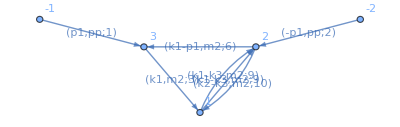

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.044553

```mathematica
toint=baik/(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify
```

-ⅈ/(π^3 x5 √(-pp^2-x5^2+2 pp (2+x5)) √(-((-4+x6) x6)) √(-(x5-x6)^2+4 x6))

```mathematica
(* the max cut of this graph contains the banana structure and an extra pole. Localizing on the pole, you get the max cut leading singularity. *)
maxcutBananatmp=maxcutBanana /. {x5 -> X6, x6 ->x5} /. X6 ->x6 //PowerExpand// FullSimplify//PowerExpand
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
```

1/(√(pp^2+(-1+x5)^2-2 pp (1+x5)) √(-4+x6) √x6 √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

-1/(π^3 (-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

```mathematica
-1/(π^3 (-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))/.pp -> 0//PowerExpand 
(*Collect[Integrate[%,x5, Assumptions->{x5 >0}], {_Log}, FullSimplify]*)
```

```mathematica
(*
Sqrt[((maxcutBananatmp/tmp)^2//FullSimplify)]//PowerExpand
*)
```

```mathematica
(* the residue in x5 around 1*)
```

```mathematica
Series[Normal[Series[(-pp^2-(-1+x5)^2+2 pp (1+x5))/(1/s-x5)/.pp -> 1/s, {s,0,2}] ]/. x5 -> 1/s, {s,0,2}]
Series[Normal[Series[(-pp^2-(-1+x5)^2+2 pp (1+x5))(*/(1/s-x5)*)/.pp -> 1/s, {s,0,2}]]/. x5 -> 1/s // Simplify, {s,0,2}]
```

10-2 s+O[s]^3

4/s-1+O[s]^3

```mathematica
Solve[-pp^2-(-1+x5)^2+2 pp (1+x5)==0,x5]
```

{{x5→1-2 √pp+pp},{x5→1+2 √pp+pp}}

```mathematica
LeadingSingularities[(Series[integrand, {x5,1,-1}]//Normal)(-1+x5)//FullSimplify//PowerExpand,{x6}]
```

{1/(4 π^3 √((-4+pp) pp))}

```mathematica
(* Notice that the same residue can be picked up by expanding in s = 1/pp for s -> 0 *)
Series[Pi^3 4 integrand /. pp-> 1/s, {s,0,7}]//PowerExpand//Normal
Residue[Series[Residue[Series[%, {x5,1,-1}], {x5,1}],{x6,0,-1}, Assumptions->x6<0]//Normal, {x6,0}]
Series[1/√((-4+pp) pp)/. pp -> 1/s, {s,0,7}]//PowerExpand
```

(4 ⅈ s)/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^2 (1+x5))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^3 (1+4 x5+x5^2))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^4 (1+x5) (1+8 x5+x5^2))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^5 (1+16 x5+36 x5^2+16 x5^3+x5^4))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^6 (1+x5) (1+24 x5+76 x5^2+24 x5^3+x5^4))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^7 (1+36 x5+225 x5^2+400 x5^3+225 x5^4+36 x5^5+x5^6))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

s+2 s^2+6 s^3+20 s^4+70 s^5+252 s^6+924 s^7

s+2 s^2+6 s^3+20 s^4+70 s^5+252 s^6+924 s^7+O[s]^8

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
ω0[ρ]/.Import["../yukawa_photon/3loop/PERIODS/omega012.m"][[1]]/. ρ^a_ /; a> 7 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824+(9671 ρ^7)/8589934592

```mathematica
(* ω0 it must come from the hard branch solution of the banana max cut *)
```

```mathematica
seriestmp=4  Collect[Series[(x5 -1)integrand Pi^3 , {pp,0,20}]//Normal // PowerExpand, {pp}, FullSimplify]/. {1/√(-4+x6) /√x6 -> roots};
expandRoot=Collect[Series[1/√(4 x6-(1-x5+x6)^2)/.x5 -> x5 , {x5,1,20}, Assumptions->{x6 < 4}], {x5},FullSimplify] ;
tmp=Residue[Series[seriestmp /. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot  /. roots -> 1/√((-4+x6) x6), {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
whatisThis=(Residue[Series[%,{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand)/. pp -> ρ /. ρ^a_ /; a >7 ->0
ω0[ρ]/.Import["../yukawa_photon/3loop/PERIODS/omega012.m"][[1]]/. ρ^a_ /; a> 7 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824+(9671 ρ^7)/8589934592

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824+(9671 ρ^7)/8589934592

```mathematica
toexpand =integrand Pi^3 (-I)16 √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2)(-1+x5) /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
seriestmp=  Collect[Collect[(Series[toexpand , {pp,0,25}]//Normal // PowerExpand) , {pp},Simplify]/(-1+x5), {pp}] ;
```

(16 ⅈ)/(√(pp^2+(-1+x5)^2-2 pp (1+x5)))

```mathematica
(*tmps1=Collect[(Series[-1/2Log[4 x6-(1-x5+x6)^2]+1/2Log[-((-4+x6) x6)], {x5,1,120}]//Normal)/.x5 -> x5m1 +1, {x5m1},Simplify];*)
```

```mathematica
(*E^(tmps1)/Sqrt[4-x6]/Sqrt[x6] /. {x5m1 -> 0.01, x6 ->1/2}
toexpandAgain=E^(tmps1);
tocheck=Normal[Series[toexpandAgain, {x5m1,0,50}]]/Sqrt[4-x6]/Sqrt[x6];*)
(*N[tocheck/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[expandRoot /.x5 -> x5m1 +1/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[1/√(4 x6-(1-x5+x6)^2) /. {x5 ->x5m1 +1}/. {x5m1 -> 10^-20, x6 ->1/2},40]*)
```

```mathematica
(*Export["./expandRoots/expandroots.m",tocheck];*)
expandRoot= Import["../yukawa_photon/3loop/expandRoots/expandroots.m"];
```

```mathematica
Print["done"]
tmp=Residue[Series[ I seriestmp/√(4 x6-(1-x5+x6)^2)/. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot /. x5m1 ->x5-1  , {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
function=(Residue[Series[tmp/√(4-x6)/Sqrt[x6],{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand) /. pp ->ρ;
```

done

```mathematica
function=Expand[function F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
ω0s=Import["../yukawa_photon/3loop/PERIODS/omega012.m"][[;;,2]];
ω0s[[1]]=Expand[ω0s[[1]] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* second derivative of period not needed *)
maxorder=2
ansatzDer=Sum[a[i] ρ^i F1[], {i,1,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,1,maxorder}] ;
inhomog=   Sum[c[i]ρ^i , {i,1,maxorder}]F1[] ω0s[[1]]+  Sum[d[i]ρ^i , {i,1,maxorder}]F1[](Expand[D[ω0s[[1]] /. extractPolySol,ρ] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ /. F2[]  -> F2[g[ρ,0]])//Expand;
```

2

```mathematica
(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand;
```

```mathematica
sol=Equal[CoefficientList[(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand,ρ,15],0]//Solve//Flatten
```

{a[2]→-a[1]/2,b[1]→2 a[1],b[2]→-a[1]/2,c[1]→-a[1],c[2]→0,d[1]→0,d[2]→-3 a[1]}

```mathematica
ansatzDersol=ansatzDer /. sol  /. F1[]-> 1 /. a[1]-> 1
inhomogSol=Sum[c[i]ρ^i , {i,1,maxorder}] ω0+  Sum[d[i]ρ^i , {i,1,maxorder}] dω0/. sol  /. F1[]-> 1 /. a[1]-> 1
```

ρ-ρ^2/2+2 ρ F1[θ]-1/2 ρ^2 F1[θ]

-3 dω0 ρ^2-ρ ω0

```mathematica
(* the differential equation is *)
(*Solve[ρ F-ρ^2/2 F+2 ρ ρ derF-1/2 ρ^2 ρ derF  +-3 dω0 ρ^2-ρ ω0 == 0,derF]*)
(* 
derF->(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ)
*)
```

```mathematica
(*the canonical candidate is given by 

(-2+d) √(-((-4+ρ) ρ)) INT[topoB,1,1,0,1,0,0,1,1,0]+1/2 (-2+d) INT[topoB,0,1,0,1,0,0,1,1,0] ((3 √ρ)/(√(4-ρ))-G3[ρ]/ω0[ρ])

*)
```

```mathematica
(* Normalize by leading singularity on max cut, it remove the F *)
```

```mathematica
(*
integrating the homogeneous part, is equivalent to integrating 
E^(-Integrate[Coefficient[(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ),F],ρ])*)
```

```mathematica
Collect[D[√((4-ρ) ρ) F[ρ]-(6 ω0[ρ] ρ)/(√(-((-4+ρ) ρ))),ρ] /.F'[ρ]-> (2 F[ρ]-6 dω0 ρ-F[ρ] ρ-2 ω0)/((-4+ρ) ρ)  /. F[ρ] -> F[ρ]/√((4-ρ) ρ)/. {ω0[ρ] -> ω0, ω0'[ρ] -> dω0}, {_F,ω0,dω0},Simplify]
```

-(2 ρ (2+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)

```mathematica
INT[topoB,1,1,0,1,0,0,1,1,0]
```

```mathematica
G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)
(* so the correction can be obtained by removing F/omega0 banana, I need something that gives me a non trivial thing along that contour (the one that gives me the holomorphic solution ) *)
```

```mathematica
Import["./Rotations/changeOfBasis22Masters_d2.m"][[22]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 (-2+d) √ρ)/(2 √(4-ρ))+((1-d/2) G3[ρ])/ω0[ρ],0,0,0,0,1}

#### 4 loop banana

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik =Pi^4  baik // FullSimplify;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.053692

```mathematica
maxcutIntegrand=baik /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} // FullSimplify // PowerExpand//FullSimplify
```

ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8)))

#### four loop triangle bubble - sunrise easy (elliptic)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik = Pi^4 baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

{-Graphics-,-Graphics-}

"Total runtime= "  0.05394

-1/(√(-(x1-x3)^2+2 (2+x1+x3) x7-x7^2) √(-(x2-x6)^2+2 (2+x2+x6) x7-x7^2) √(-(x4-x6)^2+2 (2+x4+x6) x8-x8^2) √(-pp^2-(1+x5-x8)^2+2 pp (1+x5+x8)))

```mathematica
(* max cut *)
toint=baik  /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0,x6-> 0}//FullSimplify // PowerExpand// FullSimplify
int1=Integrate[toint, x7];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]
```

-ⅈ/((-4+x7) x7 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

-ⅈ/(4 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

Banana Subcut

```mathematica
toint=baik/x6 /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify//PowerExpand//FullSimplify
```

ⅈ/(x6 √(-4+x7) √x7 √(-(x6-x7)^2+4 x7) √(-(x6-x8)^2+4 x8) √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

```mathematica
(toint x6 )/.x6 -> 0//FullSimplify//PowerExpand;
CoefficientList[Series[%, {pp,0,5}]//Normal,pp]//FullSimplify//PowerExpand//FullSimplify;
Collect[Integrate[%,x7], {_Log}, FullSimplify];
Coefficient[%,Log[4-x7]];
Series[% 4 Sqrt[3]I, {x8,1,-1}, Assumptions->Im[x8]<0]/.√(1-x8)->I Sqrt[x8-1]//Normal//PowerExpand // FullSimplify;
Residue[#,{x8,1}]&/@%
```

{1,1/3,5/27,31/243,71/729,517/6561}

```mathematica
tmp=Residue[toint I/. pp ->0//PowerExpand, {x8,1}] // FullSimplify // PowerExpand // FullSimplify
```

1/(√(-3+x6) x6 √(1+x6) √(-4+x7) √x7 √(-(x6-x7)^2+4 x7))

#### four loop triangle bubble - sunrise hard (what??)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[ π^(9/2) baik Gamma[-eps]^3/(x1^(-ν[1]) x10^ν[10] x11^ν[11] x12^ν[12] x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] x9^ν[9] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]⋀d[x9]⋀d[x10]⋀d[x11]⋀d[x12])] /. s-> pp /. eps ->0 ;
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-Graphics-,-Graphics-}

"Total runtime= "  0.118328

```mathematica
baik=baik /. {x1-> 0,x2-> 0, x3 -> 0, x4 -> 0, x5 -> 0, x6 -> 0} // PowerExpand
```

(√(3+2 pp-pp^2+2 x10+2 pp x10-x10^2-4 x12+4 pp x12-4 x10 x12-4 x12^2-4 x9-4 pp x9+4 x10 x9+8 x12 x9-4 x9^2) √(7+2 pp-pp^2+2 x10+2 pp x10-x10^2-4 x11+4 pp x11-4 x10 x11-4 x11^2-4 x12+4 pp x12-4 x10 x12-8 x11 x12-4 x12^2+8 x7-4 x8-4 pp x8+4 x10 x8+8 x11 x8+8 x12 x8-4 x8^2-4 x9-4 pp x9+4 x10 x9+8 x11 x9+8 x12 x9-8 x8 x9-4 x9^2))/(16 (-3+pp^2-pp x10+x10^2-4 pp x11+2 x10 x11+4 x11^2-4 pp x12+2 x10 x12+8 x11 x12+4 x12^2+2 pp x7+2 x10 x7-4 x11 x7-4 x12 x7+4 x7^2+2 pp x8-4 x10 x8-4 x11 x8-4 x12 x8-4 x7 x8+4 x8^2+2 pp x9-4 x10 x9-4 x11 x9-4 x12 x9-4 x7 x9+8 x8 x9+4 x9^2) (-3-2 pp+pp^2-2 x10-2 pp x10+x10^2+4 x11^2+4 x10 x11^2+4 x12-4 pp x12+4 x10 x12+4 x12^2-4 x11 x7+4 pp x11 x7-4 x10 x11 x7-8 x11 x12 x7+4 x7^2-4 x11 x8-4 pp x11 x8-4 x10 x11 x8+8 x11 x12 x8-4 x7 x8-4 pp x7 x8+4 x10 x7 x8+8 x12 x7 x8+4 x8^2+4 pp x8^2-8 x12 x8^2+4 x9+4 pp x9-4 x10 x9-8 x11^2 x9-8 x12 x9+8 x11 x7 x9+8 x11 x8 x9-8 x7 x8 x9+4 x9^2) (1-2 pp+pp^2-2 x10-2 pp x10+x10^2+4 x10 x12^2+4 x12 x9-4 pp x12 x9-4 x10 x12 x9+4 pp x9^2))

```mathematica
(baik //Denominator)
```

16 (1+pp^2+x10 (-2+x10+4 x12^2)-4 (-1+x10) x12 x9-2 pp (1+x10+2 (x12-x9) x9)) (-3+pp^2+x10^2+2 x10 (x11+x12+x7-2 (x8+x9))-pp (x10+4 x11+4 x12-2 (x7+x8+x9))+4 (x11^2+x12^2+x7^2-x7 x8+x8^2+x11 (2 x12-x7-x8-x9)-x7 x9+2 x8 x9+x9^2-x12 (x7+x8+x9))) (-3+pp^2+x10^2+4 x11^2+4 x12+x10 (-2+4 x12+4 (x11-x7) (x11-x8)-4 x9)-2 pp (1+x10+2 x12+2 (x11-x8) (-x7+x8)-2 x9)+4 x9+4 (x12^2+x7^2-x7 x8+x8^2-2 x11^2 x9-2 x7 x8 x9+x9^2-2 x12 ((x11-x8) (x7-x8)+x9)+x11 (x7+x8) (-1+2 x9)))

#### four loop triangle bubble - sunrise hard 2 (by hand 1, somehow wrong..?)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik1=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1; (* physical ones are x1 x2 x3, x4 is ISP*)
baik1=(Factor[ π^(9/2) baik1/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3])x4^ν[4] d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )]   //FullSimplify)   (* s -> (p+k1)^2 ->  x5 *) ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.034844

```mathematica
SetAttributes[sp, Orderless]
```

```mathematica
baik1=baik1 /. s-> x7;
```

```mathematica
propsecondloop={sp[k1,k1]-m2,sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x5,x6,x7}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x5,sp[k1,k2]→-k2k2/2-x5/2+x6/2,sp[k1,p1]→-m2/2-pp/2-x5/2+x7/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
baik2//FullSimplify
```

2^(4-d) (-k2p1^2+k2k2 pp)^((3-d)/2) (-4 k2p1^2 (m2+x5)+4 k2k2 pp (m2+x5)-pp (k2k2+x5-x6)^2+2 k2p1 (k2k2+x5-x6) (m2+pp+x5-x7)-k2k2 (m2+pp+x5-x7)^2)^(1/2 (-4+d))

```mathematica
(*baik1 baik2 /. d->1 /.eps -> 0//Variables*)
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik3=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1  /. x1 -> x8 /. x2 -> x9;(* physical one is x8 (actually is indifferent)*)
baik3=(Factor[ Sqrt[Pi] baik3/( x8^(-ν[1]) x9^(-ν[2])d[x8]⋀d[x9] )]   //FullSimplify) /.s -> pp
```

{{{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.028988

(ⅈ 4^eps pp^eps (-pp^2-(x8-x9)^2+2 pp (2+x8+x9))^(-1/2-eps))/Gamma[1/2-eps]

```mathematica
thirdLoopBaik
```

pp^((2-d)/2) (-x43^2+pp (m2+x6))^(1/2 (-3+d))

```mathematica
solveback=Solve[{x8 == k2k2, x9 ==  k2k2 + pp + 2 k2p1}, {k2k2,k2p1}]//Flatten
```

{k2k2→x8,k2p1→1/2 (-pp-x8+x9)}

```mathematica
baik2=baik2 /. solveback//Simplify
```

2^(4-d) (pp x8-1/4 (pp+x8-x9)^2)^((3-d)/2) (4 pp (m2+x5) x8-(m2+pp+x5-x7)^2 x8-pp (x5-x6+x8)^2-(m2+pp+x5-x7) (x5-x6+x8) (pp+x8-x9)-(m2+x5) (pp+x8-x9)^2)^(1/2 (-4+d))

```mathematica
lblBaikov=baik1 baik2 baik3/(1/Gamma[1/2-eps]^3 ⅈ 64^eps π^(7/2))/. m2 -> 1 /. d -> 2-2 eps // FullSimplify
```

4^(1+eps) pp^eps x4^eps (-(x1-x3)^2+2 (2+x1+x3) x4-x4^2)^(-1/2-eps) x7^eps (-(1+x2-x4)^2+2 (1+x2+x4) x7-x7^2)^(-1/2-eps) (pp x8-1/4 (pp+x8-x9)^2)^(1/2+eps) (4 pp (1+x5) x8-(1+pp+x5-x7)^2 x8-pp (x5-x6+x8)^2-(1+pp+x5-x7) (x5-x6+x8) (pp+x8-x9)-(1+x5) (pp+x8-x9)^2)^(-1-eps) (-pp^2-(x8-x9)^2+2 pp (2+x8+x9))^(-1/2-eps)

```mathematica
(* physical prop are x1,x2,x3 (sunrise), x5 (triangle), x6, x8 (bubble),   isp x4,x7,x9*)
```

```mathematica
lblBaikov /. eps -> 0//PowerExpand//FullSimplify
```

-((4 √(pp x8-1/4 (pp+x8-x9)^2))/(√(-(x1-x3)^2+2 (2+x1+x3) x4-x4^2) √(-(1+x2-x4)^2+2 (1+x2+x4) x7-x7^2) (-4 pp (1+x5) x8+(1+pp+x5-x7)^2 x8+pp (x5-x6+x8)^2+(1+pp+x5-x7) (x5-x6+x8) (pp+x8-x9)+(1+x5) (pp+x8-x9)^2) √(-pp^2-(x8-x9)^2+2 pp (2+x8+x9))))

```mathematica
maxcut =lblBaikov /.eps -> 0/. {x1-> 0,x2-> 0,x3-> 0, x5 -> 0, x6 -> 0, x8-> 0}//PowerExpand // FullSimplify
```

-(2 ⅈ)/(√(-((-4+x4) x4)) √(-x4^2-(-1+x7)^2+2 x4 (1+x7)) (pp-x9) √(-pp^2-x9^2+2 pp (2+x9)))

```mathematica
int1=Collect[Integrate[maxcut ,x9]//TrigToExp, _Log, PowerExpand];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]
int2=Integrate[toint2, x7]//TrigToExp;
logs =Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2, logs][[1]]
Integrate[toint3, x4]
```

1/(2 √pp √(-4+x4) √x4 √(-x4^2-(-1+x7)^2+2 x4 (1+x7)))

-ⅈ/(2 √pp √(-4+x4) √x4)

-(2 ⅈ ArcTanh[(√(-4+x4))/(2+√x4)])/(√pp)

#### four loop triangle bubble - sunrise hard 2 (by hand)

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, (k3+k4)^2-m2, (k4 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] +2sp[k3,k4] + sp[k4,k4]-m2,
sp[k4,k4] + pp + k1k1 + 2 k1p1 +2 sp[k4,P1]-m2, sp[k4,P1], sp[k3,P1]}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2,x3, x40,x41}]],sps]//Flatten;
```

{-m2+sp[k3,k3],-m2+sp[k3,k3]+2 sp[k3,k4]+sp[k4,k4],k1k1+2 k1p1-m2+pp+sp[k4,k4]+2 sp[k4,P1],sp[k4,P1],sp[k3,P1]}

```mathematica
external = {P1};
allmomenta = {P1,k3,k4};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-2-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
firstLoopBaik
```

(k1k1+2 k1p1+pp)^((2-d)/2) (-((m2+x1) x40^2)-(k1k1+2 k1p1+pp) (m2+x1) (k1k1+2 k1p1-m2+pp-x3+2 x40)-1/4 (k1k1+2 k1p1+pp) (k1k1+2 k1p1-m2+pp-x1+x2-x3+2 x40)^2+x40 (k1k1+2 k1p1-m2+pp-x1+x2-x3+2 x40) x41+(k1k1+2 k1p1-m2+pp-x3+2 x40) x41^2)^(1/2 (-4+d))

```mathematica
(*firstLoopBaik /. d-> 2 /. {x1->0, x2->0,x3->0} // FullSimplify
Integrate[%,x41]//TrigToExp;
(Coefficient[%,Log[1-(ⅈ √(-k1k1-2 k1p1+m2-pp-2 x40) (x40+2 x41))/(√(k1k1^3+8 k1p1^3-3 m2^2 pp+2 m2 pp^2+pp^3+4 m2 pp x40+4 pp^2 x40+3 m2 x40^2+5 pp x40^2+2 x40^3+4 k1p1^2 (2 m2+3 pp+4 x40)+k1k1^2 (6 k1p1+2 m2+3 pp+4 x40)+2 k1p1 (-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40))+k1k1 (12 k1p1^2-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40)+4 k1p1 (2 m2+3 pp+4 x40))))]] //FullSimplify)/.pp->-k1k1-2 k1p1+ PP*)
```

```mathematica
firstLoopBaik/.d-> 10//Variables
```

{k1k1,k1p1,pp,m2,x1,x40,x3,x2,x41}

```mathematica
(* Third loop, I have k1, k1+k2,  k1.p1 --> triangle kinematics *)
(*  
(k1)^2-m2, (k1+k2)^2-m2, (k1 + p1)^2-m2
*)
```

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x4,x5,x42}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x4,sp[k1,k2]→-k2k2/2-x4/2+x5/2,sp[k1,p1]→-m2/2-pp/2-x4/2+x42/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
```

```mathematica
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x4,x42,x5}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
```

```mathematica
propsecondloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propsecondloop , {x6,x43}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x6,sp[k2,p1]→x43}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
```

```mathematica
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10};
Variables[baik/. d-> 2]
```

{m2,x1,x7,x8,pp,x3,x4,x9,x2,x10,x5,x6}

```mathematica
baikd2=baik /. d-> 2//FullSimplify
```

16/((4 (m2+x1) x7^2+4 (m2+x1-x2+x3-2 x7) x7 x8+4 (m2+x3-2 x7) x8^2-(3 m2^2-x1^2+2 x1 (x2+x3-2 x7)+2 m2 (x1+x2+x3-2 x7)-(x2-x3+2 x7)^2+4 x7 x8+4 x8^2) x9+2 (m2+x1+x2-x3+2 x7) x9^2+x9^3) (m2^3+pp^2 x6+x4 (4 x10^2+x4 x6-2 x10 (x4-x5+x6))+m2^2 (-pp-2 x10+2 x4+x6-2 x9)+2 (-x4 x6+x10 (x4-x5+x6)) x9+x6 x9^2+pp (x4^2-2 x4 x5+(x5-x6)^2-2 x10 (x4-x5+x6)-2 x6 x9)+m2 (pp^2+4 x10^2+(x4-x9) (x4+2 x6-x9)-2 pp (x10+x5+x9)+2 x10 (-2 x4+x5-x6+x9))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0,x6->0}//FullSimplify;
```

```mathematica
int1=Collect[Integrate[maxcut ,x7]//TrigToExp, _Log, PowerExpand];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]//FullSimplify
int2 = Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2, logs][[1]]//FullSimplify//FullSimplify
```

(4 ⅈ)/(m2 √(m2-2 x8+x9) √(-((3 m2+2 x8-x9) (-x8^2+m2 x9))) (m2^2+pp^2+4 x10^2+2 x10 x9+x9^2-2 pp (x10+x9)-m2 (pp+2 (x10+x9))))

-2/(√3 m2 √(m2-2 x8+x9) √(-((3 m2+2 x8-x9) (-x8^2+m2 x9))) √(m2^2+(pp-x9)^2-2 m2 (pp+x9)))

(2 ⅈ)/(√3 √(-4+x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(-x9+1/4 (-3+x8+x9)^2))

```mathematica
K3banana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6))) /. {x6 -> x9, x5 -> x8} //Expand // FullSimplify
((toint3 Sqrt[3] /2(-I)/. m2->1 //Expand // FullSimplify) /. x8 -> x8/2  /.x8 -> x8 -3 + x9//FullSimplify // PowerExpand//FullSimplify//PowerExpand ) /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]/.x8 -> x8 +4 /. x8 -> -x8//FullSimplify//PowerExpand
```

1/(√(-4+x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

-(2 ⅈ)/(√(4-x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))